```mathematica
<<UNET`
```

## Generated Data

### Show UNET s

```mathematica
dim={32,112,112};
```

```mathematica
MakeUNET[1,8,32,dim,DropOutRate->.5,BlockType->"UNET"]
```

```mathematica
MakeUNET[1,8,32,dim,DropOutRate->.5,BlockType->"UResNet"]
```

```mathematica
MakeUNET[1,8,32,dim,DropOutRate->.5,BlockType->"ResNet"]
```

```mathematica
MakeUNET[1,8,{4,2},dim,DropOutRate->.5,BlockType->"UDenseNet"]
```

```mathematica
MakeUNET[1,8,{4,2},{128,128},DropOutRate->.5,BlockType->"DenseNet"]
```

### Describe UNET

```mathematica
style={Bold,TextAlignment->Center,FontFamily->"Helvetica"};
lab=Style[#,style]&/@{"n or (n, r)",
 "Unet", "UResNet", "ResNet", "UDenseNet", "DenseNet"};
```

```mathematica
CountConv=Count[Head/@NetInformation[#,"LayersList"],ConvolutionLayer]&;
```

```mathematica
(*parameters*)
dim2D={112,112};
dim3D={32,112,112};
{nchan,nclass}={4,8};

dep={8,16,24,32,48,64};
depD={{2,4},{4,4},{6,4},{8,4},{12,4},{16,4}};
par=Table[ToString[dep[[i]]]<>" or ("<>ToString[depD[[i,1]]]<>","<>ToString[depD[[i,2]]]<>")",{i,1,Length[dep]}];
```

```mathematica
(*2D UNET generation*)
par2D=Table[
nets2D=MapThread[MakeUNET[nchan,nclass, #2[[i]],dim2D,BlockType->#1 ]&,{{"UNET","UResNet","ResNet","UDenseNet","DenseNet"},{dep,dep,dep,depD,depD}}];
Flatten@{par[[i]],NetInformation[#,"ArraysTotalElementCount"]&/@nets2D}
,{i,1,Length[dep]}];

tab1=Column[{Style["2D Nets - Numer of Array Elementes",style],TableForm[par2D,TableHeadings->{None,lab},TableAlignments->Right]},Alignment->Center];
```

```mathematica
(*3D UNET generation*)
par3D=Table[nets3D=MapThread[MakeUNET[nchan,nclass, #2[[i]],dim3D,BlockType->#1 ]&,{{"UNET","UResNet","ResNet","UDenseNet","DenseNet"},{dep,dep,dep,depD,depD}}];
Flatten@{par[[i]],NetInformation[#,"ArraysTotalElementCount"]&/@nets3D}
,{i,1,Length[dep]}];

tab2=Column[{Style["3D Nets - Numer of Array Elementes",style],TableForm[par3D,TableHeadings->{None,lab},TableAlignments->Right]},Alignment->Center];
```

```mathematica
layers2D=ToString[CountConv[#]]&/@nets2D;
layers3D=ToString[CountConv[#]]&/@nets3D;
layers=Style["Number of convolution layers\n"<>"1)  UNet: "<>layers2D[[1]]<>"    2)  UResNet: "<>layers2D[[2]]<>
"    3)  ResNet: "<>layers2D[[3]]<>"    4)  UDenseNet: "<>layers2D[[4]]<>"    5)  DenseNet: "<>layers2D[[5]],style];
```

```mathematica
Column[{layers,"",tab1,"",tab2},Alignment->Center]
```

Number of convolution layers
1)  UNet: 20    2)  UResNet: 20    3)  ResNet: 29    4)  UDenseNet: 90    5)  DenseNet: 174

2D Nets - Numer of Array Elementes
n or (n, r) | Unet | UResNet | ResNet | UDenseNet | DenseNet
8 or (2,4) | 494576 | 248280 | 277384 | 52560 | 29944
16 or (4,4) | 1970648 | 987304 | 1100040 | 202904 | 110760
24 or (6,4) | 4428224 | 2217080 | 2467976 | 451040 | 242456
32 or (8,4) | 7867304 | 3937608 | 4381192 | 796968 | 425032
48 or (12,4) | 17689976 | 8850920 | 9843464 | 1782200 | 942824
64 or (16,4) | 31438664 | 15727240 | 17486856 | 3158600 | 1664136

3D Nets - Numer of Array Elementes
n or (n, r) | Unet | UResNet | ResNet | UDenseNet | DenseNet
8 or (2,4) | 1476080 | 739032 | 413704 | 149328 | 54136
16 or (4,4) | 5896664 | 2950312 | 1645320 | 589976 | 207528
24 or (6,4) | 13261760 | 6633848 | 3694856 | 1321952 | 460184
32 or (8,4) | 23571368 | 11789640 | 6562312 | 2345256 | 812104
48 or (12,4) | 53024120 | 26517992 | 14750984 | 5265848 | 1813736
64 or (16,4) | 94254920 | 47135368 | 26211336 | 9351752 | 3212424

### Examples of Test Data

```mathematica
{data,label}=CreateImage1[];
Flatten@{MakeChannelImage[data],Image[label]}
```

{-Graphics-,-Graphics-}

```mathematica
{data,label}=CreateImage2[];
Flatten@{MakeChannelImage[data],MakeClassImage[label]}
```

{-Graphics-,-Graphics-}

```mathematica
{data,label}=CreateImage3[];
Flatten@{MakeChannelImage[data],MakeClassImage[label,{1,4}]}
```

{-Graphics-,-Graphics-}

```mathematica
{data,label}=CreateImage4[];
Flatten@{MakeChannelImage[data],MakeClassImage[label,{1,4}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Test Cases 1: 1 channel - 1 classes

```mathematica
(*make test data*)
{data1,label1}=MakeTestImages[100,1];
```

```mathematica
(*split the data*)
{train1,valid1,testData1,testLabel1,order1}=SplitTrainData[data1,label1];
```

Dimensions data: {100,1,128,128} - Dimensions label: {100,128,128}

Nuber of Samples in each set: {70,20,10}

```mathematica
(*visualize the test data*)
ShowChannelClassData[testData1,testLabel1, NumberRowItems->3,MakeDifferenceImage->False,StepSize->2]
```

channels: 1 - classes: 1 - Dimensions :{128,128}

Evaluating test data

DICE per class: {1→1.}

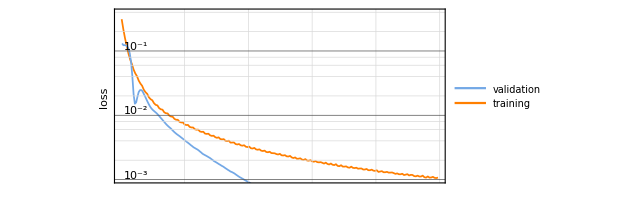

```mathematica
(*train the net*)
{{net1,trained1,netTrained1},{plots1,result1,iou1}}=TrainUNET[train1,valid1,{testData1,testLabel1},
TargetDevice->{"GPU",1},MaxTrainingRounds->250,NetParameters->16,DropOutRate->.5];
plots1
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData1,netTrained1]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData1,testLabel1,result1, NumberRowItems->3,MakeDifferenceImage->False,StepSize->1]
```

```mathematica
(*visualize the test data with diff image*)
ShowChannelClassData[testData1,testLabel1,result1, NumberRowItems->3,MakeDifferenceImage->True,StepSize->1]
```

### Test Case 2: 1 channel - 2 classes

```mathematica
(*make test data*)
{data2,label2}=MakeTestImages[100,2];
```

```mathematica
(*split the data*)
{train2,valid2,testData2,testLabel2,order}=SplitTrainData[data2,label2];
```

Dimensions data: {100,1,128,128} - Dimensions label: {100,128,128}

Nuber of Samples in each set: {70,20,10}

channels: 1 - classes: 2 - Dimensions :{128,128}

Evaluating test data

DICE per class: {1→0.998,2→0.991}

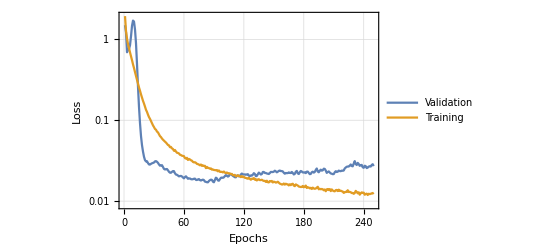
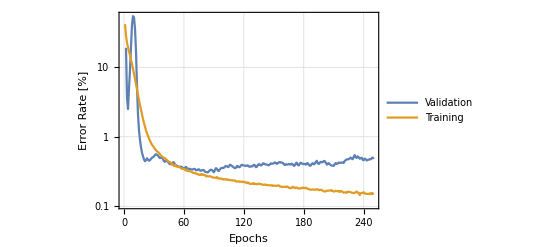

```mathematica
(*train the net*)
{{net2,trained2,netTrained2},{plots2,result2,iou2}}=TrainUNET[train2,valid2,{testData2,testLabel2},
TargetDevice->{"GPU",1},MaxTrainingRounds->250,NetParameters->16,DropOutRate->0.5];
plots2
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData2,netTrained2]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData2, testLabel2,result2, NumberRowItems->3,MakeDifferenceImage->True,StepSize->1]
```

### Test Case 3: 1 channel - 4 classes

```mathematica
(*make test data*)
{data3,label3}=MakeTestImages[150,3];
```

```mathematica
(*data augmentation, increase the data by flipping and rotating*)
(*visualize the flips and rotations*)
data3R=RotateFlip[data3[[1;;2]]];
label3R=RotateFlip[label3[[1;;2]]];
ShowChannelClassData[data3R,label3R, NumberRowItems->4,MakeDifferenceImage->False,StepSize->1,ImageSize->200]
```

```mathematica
(*split the data*)
{train3,valid3,testData3,testLabel3,order3}=SplitTrainData[data3,label3,AugmentTrainData->False];
```

Dimensions data: {150,1,128,128} - Dimensions label: {150,128,128}

Nuber of Samples in each set: {105,30,15}

channels: 1 - classes: 4 - Dimensions :{128,128}

Evaluating test data

DICE per class: {1→1.,2→0.868,3→0.94,4→0.998}

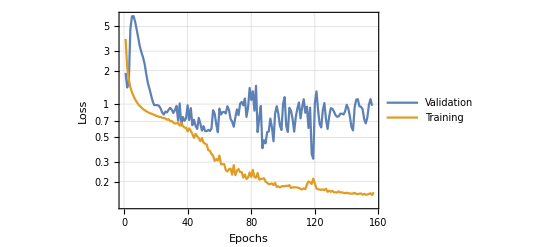
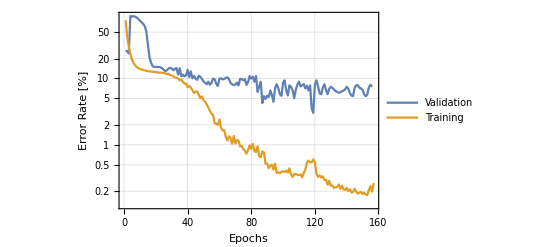

```mathematica
(*train the net*)
{{net3,trained3,netTrained3},{plots3,result3,iou3}}=TrainUNET[train3,valid3,{testData3,testLabel3},
TargetDevice->{"GPU",1},MaxTrainingRounds->250,NetParameters->32,BlockType->"ResNet",DropOutRate->0.50];
plots3b
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData3,netTrained3]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData3, testLabel3, result3, NumberRowItems->3,MakeDifferenceImage->True,StepSize->1]
```

### Test Case 4 : 3 channels - 4 classes

```mathematica
(*make test data*)
{data4,label4}=MakeTestImages[100,4];
```

```mathematica
(*split the data*)
{train4,valid4,testData4,testLabel4,order4}=SplitTrainData[data4,label4];
```

Dimensions data: {100,3,128,128} - Dimensions label: {100,128,128}

Nuber of Samples in each set: {70,20,10}

channels: 3 - classes: 4 - Dimensions :{128,128}

Evaluating test data

DICE per class: {1→1.,2→0.999,3→0.999,4→0.996}

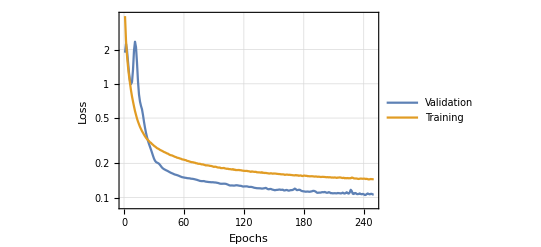
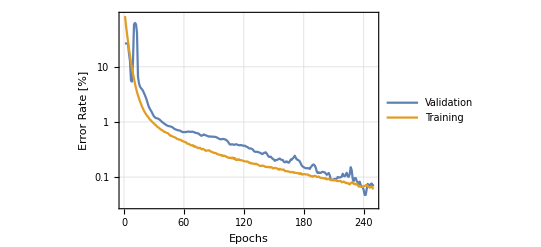

```mathematica
(*train the net*)
{{net4,trained4,netTrained4},{plots4,result4,iou4}}=TrainUNET[train4,valid4,{testData4,testLabel4},
TargetDevice->{"GPU",1},MaxTrainingRounds->250,NetParameters->32,BlockType->"ResNet",DropOutRate->0.5];
plots4
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData4,netTrained4]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData4, testLabel4, result4, NumberRowItems->2,MakeDifferenceImage->True,StepSize->1,ImageSize->650]
```

### Test Case 5 - same as 4 with animation

```mathematica
{data5,label5}=MakeTestImages[100,4];
```

```mathematica
{train5,valid5,testData5,testLabel5,order}=SplitTrainData[data5,label5];
```

Dimensions data: {100,3,128,128} - Dimensions label: {100,128,128}

Nuber of Samples in each set: {70,20,10}

```mathematica
(*choose a nice image*)
MakeChannelImage/@testData5
```

```mathematica
im=2;nchan=Max[testLabel5];solutions={};
imChan=First@MakeChannelImage[testData5[[im,{1}]]];
(*The monitoring function*)
monitor=AppendTo[solutions,ClassDecoder[NetExtract[#Net,"net"][testData5[[im]],TargetDevice->"GPU"],nchan]]&;

(*train the net with monitor function*)
{{net,trained,netTrained},{plots,result,iou}}=TrainUNET[train5,valid5,{testData5,testLabel5},
 TargetDevice->{"GPU",1},MaxTrainingRounds->100,NetParameters->32,DropOutRate->.5,
BlockType->"ResNet",TrainingProgressFunction->{monitor,"Interval"->Quantity[1,"Batches"]}];
```

channels: 3 - classes: 4 - Dimensions :{128,128}

Evaluating test data

DICE per class: {1→0.996,2→0.976,3→0.993,4→0.938}

```mathematica
(*make the animation images*)
solIm=ColorReplace[MakeClassImage[#,{1,4}],ColorData["Rainbow"][0]]&/@solutions;
anim=Table[Show[ImageCompose[imChan,{sol,.5}],ImageSize->500],{sol,solIm}];
```

```mathematica
(*play the animatin*)
Animate[im,{im,anim}]
```

```mathematica
Export["anim.gif",anim,"DisplayDuration"->.2,"AnimationRepetitions"->Infinity]
```

anim.gif